# APPM 2350 Project #2

### By Davis Landry, Mahalie Hill, Mia Miller

## 3 Defining the Mountain Range

-Graphics3D-

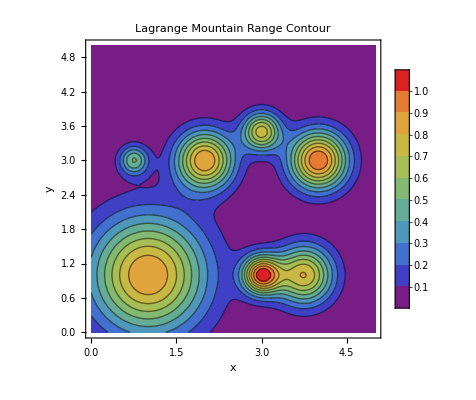

```mathematica
mR = {{{1,1},1,.9},{{3,1},3,1},{{3.75,1},2,.8},{{4,3},2,1},{{3,3.5},3,.75},{{2,3},2,.9},{{.75,3},4,.5}};

gaussian[ϵ_,r_] = E^(-(ϵ*r)^2);
m[x_,y_] := Sum[mR[[i,3]]* gaussian[mR[[i,2]],Sqrt[(Sqrt[(mR[[i,1,1]]-x)^2 + (mR[[i,1,2]]-y)^2])^2]],{i,7}];

mountainPlot3D = Plot3D[m[x,y],{x,0,5},{y,0,5}, AxesLabel->{"x","y","z"}, PlotLabel->"Lagrange Mountain Range", ColorFunction->"Rainbow"]

mountainContour = ContourPlot[m[x,y],{x,0,5},{y,0,5}, PlotLegends->Automatic, ColorFunction->"Rainbow",Frame->{True,True,False,False},FrameLabel->Automatic, PlotLabel->"Lagrange Mountain Range Contour", Contours->10]
```

## 4 Analyzing the Mountain Range

Plotting Paths

-Graphics3D-

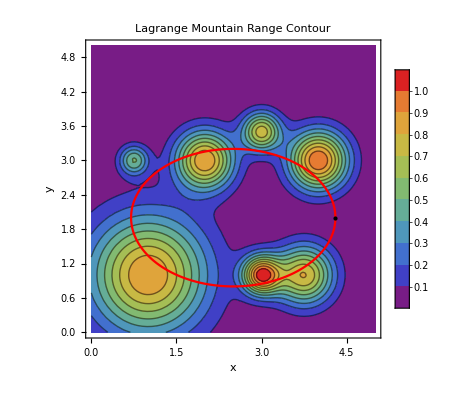

```mathematica
mt[t_] :=Sum[mR[[i,3]]* gaussian[mR[[i,2]],Sqrt[(Sqrt[(mR[[i,1,1]]-(2.5 + 1.8Cos[4t]))^2 + (mR[[i,1,2]]-(2+1.2Sin[4t]))^2])^2]],{i,7}];

r[t_] := {2.5 + 1.8Cos[4t], 2+1.2Sin[4t]};
r3D[t_] := {2.5 + 1.8Cos[4t], 2+1.2Sin[4t],m[2.5 + 1.8Cos[4t], 2+1.2Sin[4t]]};

path3D = ParametricPlot3D[r3D[t],{t,0,π/2}, PlotStyle->{Red,Thickness[.01]}];
path = ParametricPlot[r[t],{t,0,π/2}, PlotStyle->Red];

point3D = Graphics3D[{PointSize[Large],Point[r3D[0]]}];
point = Graphics[{PointSize[Large],Black,Point[r[0]]}];

Show[{mountainPlot3D  ,path3D,point3D}]
Show[{mountainContour,path    ,point}]
```

Honey Badger (WRONG)

```mathematica
gradr3D[t_] := {-7.2Sin[4 t],4.8 Cos[4 t],mt'[t]};
Norm[gradr3D[π/4]]
mt'[π/4]
```

5.61019

2.90417

Change of Elevation

14.7402

-8.97206

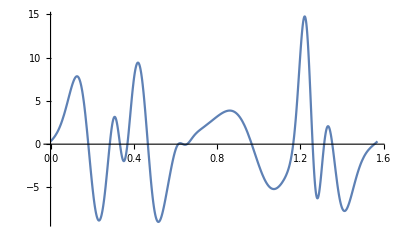

```mathematica
dVals = Table[mt'[t],{t,0,π/2,π/20000}];

Max[dVals]
Min[dVals]
Plot[mt'[t],{t,0,π/2}]
```

Highest Elevation(use lagrange multipliers)

0.934483

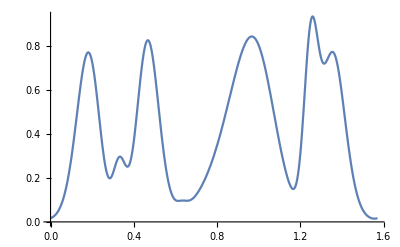

```mathematica
elevVals =Table[mt[t],{t,0,π/2,π/20000}];
Max[elevVals]
Plot[mt[t],{t,0,π/2}]
```

Thus the highest point is at 7934 ft above sea level.

Lake Mochi

Rock inside of trail

Clairautnium

```mathematica
delta[x_,y_,z_] := E^(-.25((x-2.5)^2+(y-2.5)^2+(z-.2)^2));
NIntegrate[delta[x,y,z],{x,0,5},{y,0,5},{z,0,m[x,y]}]
```

2.51448